## Start

### Setup

#### Default options for plots, error messages, and colors

```mathematica
SetDirectory["/Users/gabrielpatenotte/Documents/Research/Ni Group/Mathematica"];
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black]; 
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""}]; 
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
colors=RGBColor/@{"#408EC6","#7A2048","#1E2761","#89ABE3FF","#EA738DFF","#8BB9B9"};
```

SetDirectory::cdir: Cannot set current directory to /Users/gabrielpatenotte/Documents/Research/Ni Group/Mathematica.

#### Basis labels

```mathematica
bUC={"I1","mI1","I2","mI2","N","mN","S","mS"};
bI={"I1","I2","I","mI","N","mN","S","mS"};
bJ={"I1","mI1","I2","mI2","N","S","J","mJ"};
bIJ={"I1","I2","I","mI","N","S","J","mJ"};
bF={"I1","I2","I","N","S","J","F","mF"};
bF1={"I1","I2","mI2","N","F1","mF1","S","J"};
bF2={"I1","mI1","I2","N","F2","mF2","S","J"};
bN={"N","mN"};
bI1={"I1","mI1"};
bI2={"I2","mI2"};
bS={"S","mS"};
b={bUC,bI,bJ,bIJ,bF,bF1,bF2,bN};
```

#### Supporting functions

```mathematica
conj[x_]:=Module[{re,im},x/.(Complex[re_,im_]->Complex[re,-im])]; (*Replacement that gives the complex conjugate*)
createSpace[aQN_Association]:=Module[{a},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
nℋ=Sum[(2I1+1)(2I2+1)(2N+1)(2S+1),{N,a["N"]},{S,a["S"]},{I1,a["I1"]},{I2,a["I2"]}]; (*number of states in Hilbert space*)
ℋ=IdentityMatrix[nℋ];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
nℋI1=(2a["I1"][[1]]+1);
nℋI2=(2a["I2"][[1]]+1);
nℋI=(2a["I1"][[1]]+1)(2a["I2"][[1]]+1);
nℋS=(2a["S"][[1]]+1);
nℋN=Sum[(2N+1),{N,a["N"]}];
ℋ=IdentityMatrix[nℋ];
ℋI1=IdentityMatrix[nℋI1];
ℋI2=IdentityMatrix[nℋI2];
ℋI=IdentityMatrix[nℋI];
ℋS=IdentityMatrix[nℋS];
ℋN=IdentityMatrix[nℋN];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
sℋI1=Partition[ℋI1,{nℋI1,1}][[1]];
sℋI2=Partition[ℋI2,{nℋI2,1}][[1]];
sℋI=Partition[ℋI,{nℋI,1}][[1]];
sℋS=Partition[ℋS,{nℋS,1}][[1]];
sℋN=Partition[ℋN,{nℋN,1}][[1]];
] (*example: aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->{0,1}]*)
```

SetDelayed::write: Tag Rule in (Complex[a_,b_]→Complex[a,{{-I1,-mI1,-I2,-mI2,-N,-mN,-S,-mS},{-I1,-I2,-I,-mI,-N,-mN,-S,-mS},{-I1,-mI1,-I2,-mI2,-N,-S,-J,-mJ},{-I1,-I2,-I,-mI,-N,-S,-J,-mJ},{-I1,-I2,-I,-N,-S,-J,-F,-mF},{-I1,-I2,-mI2,-N,-F1,-mF1,-S,-J},{-I1,-mI1,-I2,-N,-F2,-mF2,-S,-J},{-N,-mN}}])[x_] is Protected.

```mathematica
createLists[aQN_Association]:=Module[{a,spins},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
am={{I1,a["I1"]},{I2,a["I2"]},{S,a["S"]},{N,a["N"]}}; (*angular momentums*)
lUC=Flatten[Table[ToExpression[bUC],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{mS,-S,S},{mN,-N,N}],7];
lI=Flatten[Table[ToExpression[bI],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{mN,-N,N},{mS,-S,S}],7];
lJ=Flatten[Table[ToExpression[bJ],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lIJ=Flatten[Table[ToExpression[bIJ],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lF=Flatten[Table[ToExpression[bF],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{J,Abs[N-S],N+S},{F,Abs[I-J],I+J},{mF,-F,F}],7];
lF1=Flatten[Table[ToExpression[bF1],Evaluate[Sequence@@am],{mI2,-I2,I2},{J,Abs[N-S],N+S},{F1,Abs[I1-J],I1+J},{mF1,-F1,F1}],7];
lF2=Flatten[Table[ToExpression[bF2],Evaluate[Sequence@@am],{mI1,-I1,I1},{J,Abs[N-S],N+S},{F2,Abs[I2-J],I2+J},{mF2,-F2,F2}],7];
lN=Flatten[Table[ToExpression[bN],{N,a["N"]},{mN,-N,N}],1];
l = {lUC,lI,lJ,lIJ,lF,lF1,lF2,lN};
BtoL = AssociationThread[b->l];
LtoB = AssociationThread[l->b];
StoLN=AssociationThread[sℋN->lN];
LtoSN=AssociationThread[lN->sℋN];
yN=lN/.{n_,mn_}->SphericalHarmonicY[n,mn,θ,ϕ];
]
```

### Functions

```mathematica
eig[Hn_]:=Chop[Sort[Eigensystem[Hn]ᵀ]ᵀ];
reorder[list_,order_]:=Part[order,list];
VtoQN[eigenvector_,basis_:bUC,populationThreshold_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eigenvector,Abs[#]^2>=populationThreshold&],Abs];
sP=Position[eigenvector,#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,BtoL[basis][[sP]]}]
QNtoS[rep_,basis_:bUC]:=With[{labels=rep[[All,1]],numbers=rep[[All,2]]},Flatten[Position[BtoL[basis][[All,Flatten[labels/.PositionIndex[basis]]]],numbers]]]
QNtoV[rep_,eigenvectors_,basis_:bUC]:=Module[{pos,eigs},pos=QNtoS[rep];eigs=OrderingBy[eigenvectors[[All,pos]],Total[Abs[#]^2]&][[-Length[pos];;-1]];eigs]
reduceV[vecs_,param_,s_,rep_]:=Module[{pos,l},
pos=Flatten[Position[bUC,#]&/@rep[[All,1]]];
l=Transpose@{lUC[[All,pos]],Abs[vecs[[param,s]]]^2};
l=Map[{#[[1,1]],Total[#[[All,2]]]}&,GatherBy[l,First]];
l[[All,2]]
]
```

### Load

```mathematica
aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->Range[0,1]];
createSpace[aQN] (*creates a Hilbert space*)
createLists[aQN] (*creates a list of the quantum numbers of each basis state*)
HacN=Import["HacN.m"][[1;;Length[lN],1;;Length[lN]]]; 
(*needs to be multiplied by U*)
```

### Hamiltonians

#### Rotational Hamiltonian

```mathematica
HN=DiagonalMatrix[(#(#+1))&/@lN[[All,1]]]; (*needs to be multiplied by B*)
H0=U HacN+B HN;
```

```mathematica
model[θq_,U_,B_,θoffset_]=Collect[FullSimplify[eig[H0][[1,4]]],U]/.{αpar->1872.1153,αperp->467.0375,θq->θq+θoffset}
```

2 B+0.000071271 U (-1405.08+4215.23 Cos[2 (θoffset+θq)])

```mathematica
fValon=2670;
countLinear=1061340;
```

```mathematica
data={{559864,0.5,Around[801.492,0.005]},{531420,0.5,Around[801.294,0.004]},{545642,.5,Around[801.396,0.003]},{552753,.5,Around[801.440,0.003]},{540804,0.18,Around[801.323,0.007]},{540804,2,Around[801.45,0.01]},{540804,2.5,Around[801.502,0.006]},{Round[540804-14222.222*0.15],2.5,Around[801.41,0.01]},{Round[540804-14222.22*0.15],0.18,Around[801.339,0.003]},{Round[540804-14222.22*0.15],2.5,Around[801.397,0.004]},{Round[540804-14222.22*0.2],0.18,Around[801.332,0.003]},{Round[540804-14222.22*0.2],2.5,Around[801.379,0.005]},{Round[540804-14222.22*0.3],0.18,Around[801.325,0.008]},{Round[540804-14222.22*0.3],2.5,Around[801.320,0.003]},{Round[540804-14222.22*0.4],0.18,Around[801.326,0.008]},{Round[540804-14222.22*0.4],2.5,Around[801.266,0.004]},{515000,0.18,Around[801.292,0.003]},{515000,2.5,Around[800.491,0.007]},{555000,2.5,Around[802.018,0.004]},{555000,0.18,Around[801.375,0.005]},{555000,1.34,Around[801.691,0.004]},{515000,1.34,Around[800.885,0.005]},{537000,1.34,Around[801.33,0.01]},{679222,0.18,Around[801.591,0.003]},{394778,0.18,Around[801.099,0.004]},{394778,0.5,Around[800.498,0.002]}};
data[[All,3]]=(data[[All,3]]+fValon)10^6;
data[[All,1]]=π/180(countLinear-data[[All,1]])/14222.222;
```

```mathematica
dataODT134=Select[data,#[[2]]==1.34&][[All,{1,3}]];
dataODT050=Select[data,#[[2]]==0.5&][[All,{1,3}]];
dataODT018=Select[data,#[[2]]==0.18&][[All,{1,3}]];
dataODT250=Select[data,#[[2]]==2.5&][[All,{1,3}]];
```

```mathematica
countODT018=dataODT018[[All,1]];
freqODT018=#["Value"]&/@dataODT018[[All,2]];
errorODT018=#["Uncertainty"]&/@dataODT018[[All,2]];
countODT250=dataODT250[[All,1]];
freqODT250=#["Value"]&/@dataODT250[[All,2]];
errorODT250=#["Uncertainty"]&/@dataODT250[[All,2]];
countODT134=dataODT134[[All,1]];
freqODT134=#["Value"]&/@dataODT134[[All,2]];
errorODT134=#["Uncertainty"]&/@dataODT134[[All,2]];
countODT050=dataODT050[[All,1]];
freqODT050=#["Value"]&/@dataODT050[[All,2]];
errorODT050=#["Uncertainty"]&/@dataODT050[[All,2]];
```

```mathematica
nlmODT018=NonlinearModelFit[Transpose@{countODT018,freqODT018},{model[θq,U,B,θoffset],-π/4<=θoffset<π/4},{U,{B,1.736*^9},{θoffset,0}},θq,Weights->1/errorODT018^2];
nlmODT050=NonlinearModelFit[Transpose@{countODT050,freqODT050},{model[θq,U,B,θoffset],-π/4<=θoffset<π/4},{U,{B,1.736*^9},{θoffset,0}},{θq},Weights->1/errorODT050^2];
nlmODT134=NonlinearModelFit[Transpose@{countODT134,freqODT134},{model[θq,U,B,θoffset],-π/4<=θoffset<π/4},{U,{B,1.736*^9},{θoffset,0}},{θq},Weights->1/errorODT134^2];
nlmODT250=NonlinearModelFit[Transpose@{countODT250,freqODT250},{model[θq,U,B,θoffset],-π/4<=θoffset<π/4},{U,{B,1.736*^9},{θoffset,0}},{θq},Weights->1/errorODT250^2];
```

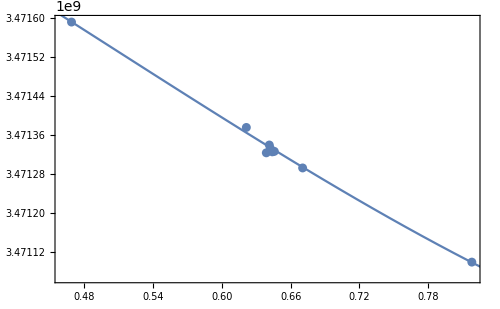

```mathematica
Show[ListPlot[{dataODT018},PlotRange->All,ImagePadding->Automatic],Plot[nlmODT018[θ],{θ,π/180 15,π/180 55},PlotStyle->Automatic]]
```

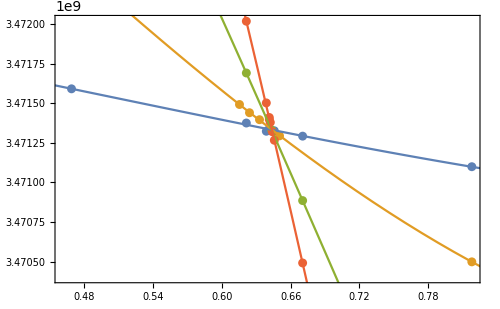

```mathematica
Show[ListPlot[{dataODT018,dataODT050,dataODT134,dataODT250},PlotRange->All,ImagePadding->Automatic],Plot[{nlmODT018[θ],nlmODT050[θ],nlmODT134[θ],nlmODT250[θ]},{θ,π/180 15,π/180 55},PlotStyle->Automatic]]
```

```mathematica
paramsODT018=nlmODT018["BestFitParameters"]
errorsODT018=nlmODT018["ParameterErrors"]
paramsODT250=nlmODT250["BestFitParameters"]
errorsODT250=nlmODT250["ParameterErrors"]
paramsODT050=nlmODT050["BestFitParameters"]
errorsODT050=nlmODT050["ParameterErrors"]
paramsODT134=nlmODT134["BestFitParameters"]
errorsODT134=nlmODT134["ParameterErrors"]
nlmODT018["ParameterTable"]
nlmODT050["ParameterTable"]
nlmODT134["ParameterTable"]
nlmODT250["ParameterTable"]
```

{U→2.49905×10^6,B→1.7359×10^9,θoffset→0.283946}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{67382.2,38518.4,0.0467566}

{U→5.71253×10^7,B→1.7349×10^9,θoffset→-0.0765797}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{8.00848×10^6,2.41607×10^6,0.148479}

{U→1.10541×10^7,B→1.73714×10^9,θoffset→0.434815}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{977151.,261393.,0.0478342}

{U→2.77397×10^7,B→1.73633×10^9,θoffset→0.0543459}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::dof: The number of parameters 3 is not less than the number of data values 3. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

Missing[]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
U | 2.49905×10^6 | 67382.2 | 37.0877 | 2.56427×10^-8
B | 1.7359×10^9 | 38518.4 | 45066.7 | 8.05691×10^-27
θoffset | 0.283946 | 0.0467566 | 6.07284 | 0.000905272

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
U | 1.10541×10^7 | 977151. | 11.3126 | 0.00772365
B | 1.73714×10^9 | 261393. | 6645.7 | 2.26422×10^-8
θoffset | 0.434815 | 0.0478342 | 9.09005 | 0.0118869

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::dof: The number of parameters 3 is not less than the number of data values 3. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

Missing[]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
U | 5.71253×10^7 | 8.00848×10^6 | 7.1331 | 0.000840521
B | 1.7349×10^9 | 2.41607×10^6 | 718.066 | 9.94196×10^-14
θoffset | -0.0765797 | 0.148479 | -0.515761 | 0.628009

```mathematica
odtData={{0.18,Around[U,errorsODT018[[1]]]/.paramsODT018},{0.5,Around[U,errorsODT050[[1]]]/.paramsODT050},{1.34,Around[U,errorsODT134[[1]]]/.paramsODT134},{2.50,Around[U,errorsODT250[[1]]]/.paramsODT250}};
```

```mathematica
odtDataNoError={{0.18,U/.paramsODT018},{0.5,U/.paramsODT050},{1.34,U/.paramsODT134},{2.50,U/.paramsODT250}};
odtDataError={errorsODT018[[1]],errorsODT050[[1]],errorsODT134[[1]],errorsODT250[[1]]};
```

```mathematica
b=.
```

```mathematica
nlmODTdata=NonlinearModelFit[odtDataNoError,a amp +b,{a,b},{amp},Weights->1/odtDataError^2];
```

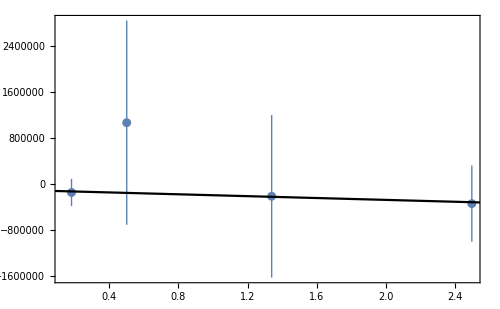

```mathematica
Show[ListPlot[odtData,PlotRange->All],Plot[nlmODTdata[x],{x,-.5,3}]]
```

```mathematica
nlmODTdata[0.1]
```

-123136.